### 导入训练数据

```mathematica
imageSet="/Users/yanbozhang/项目 & 存档/02 设计项目/神奇秘谱重制/图库/5. 单字切割/Full_Set";
```

```mathematica
imageFileList={"0001","0010","0014","0018","0024","0026","0033","0036","0037","0042"};
imageList=Import[imageSet<>"/"<>#<>".png"]&/@imageFileList
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 标记锚点

### 函数

```mathematica
Mark[img_]:=
DynamicModule[{outline={},marks={},ol=True},
Panel[
Grid[
{
{Button["Save",Return[{outline,marks}]]},{Button["Clear",outline={};marks={};ol=True]},{Button["Mark",ol=False]},
{ClickPane[Dynamic@Show[img,Graphics[{Hue[0.2,0.7,0.7,0.5],EdgeForm[Dashed],Polygon[outline],Orange,Disk[#,3]&/@outline,Green,Line[marks],Disk[#,3]&/@marks}]],If[ol,AppendTo[outline,#],AppendTo[marks,#]]&]}
}
]
]
]
```

```mathematica
MarkList[imglist_,index_,dataset_]:=
DynamicModule[{outline={},marks={},ol=True},
Panel[
Grid[
{
{Button["Save",ToExpression[dataset<>"[["<>ToString[index]<>"]]="<>ToString[{outline,marks}]]]},{Button["Clear",outline={};marks={};ol=True]},{Button["Mark",ol=False]},
{ClickPane[Dynamic@Show[imglist⟦index⟧,Graphics[{Hue[0.2,0.7,0.7,0.5],EdgeForm[Dashed],Polygon[outline],Orange,Disk[#,3]&/@outline,Green,Line[marks],Disk[#,3]&/@marks}]],If[ol,AppendTo[outline,#],AppendTo[marks,#]]&]}
}
]
]
]
```

### 标记

```mathematica
points=Table[{},{Length[imageList]}]
```

{{},{},{},{},{},{},{},{},{},{}}

```mathematica
Short/@points
```

{{{{73.5742,118.483},{119.164,130.546},«11»,{92.3047,140.581}},{«1»}},{{{86.0508,78.8545},{116.313,86.4014},«11»,{88.293,87.2568}},{«1»}},{{{78.8906,119.804},{121.875,131.296},«11»,{89.4844,136.284}},{«1»}},{{{86.3906,78.8545},{129.57,89.2998},«11»,{89.8203,87.3584}},{«1»}},{{{78.4883,114.897},{119.164,126.456},«11»,{91.8906,139.28}},{«1»}},{{{85.8867,83.124},{119.613,92.0459},«11»,{86.6836,89.0576}},{«1»}},{{{81.8555,118.706},{120.656,134.483},«11»,{89.2344,139.886}},{«1»}},{{{84.5195,121.116},{116.547,129.241},«11»,{92.3984,138.722}},{«1»}},{{{78.0313,90.4873},{120.594,99.0186},«11»,{89.4023,101.901}},{«1»}},{{{88.9375,98.1904},{119.609,110.019},«11»,{90.5898,109.812}},{«1»}}}

```mathematica
Length/@#&/@points
```

{{14,3},{14,3},{14,3},{14,3},{14,3},{14,3},{14,3},{14,3},{14,3},{14,3}}

```mathematica
Export[NotebookDirectory[]<>"points.mx",points]
```

/Users/yanbozhang/项目 & 存档/02 设计项目/神奇秘谱重制/半自动重制/points.mx

```mathematica
MarkList[imageList,10,"points"]
```

```mathematica
RotationOneData[θ_,d_]:={RotationTransform[θ,{10,10}]/@d⟦1⟧,RotationTransform[θ,{10,10}]/@d⟦2⟧}
```

```mathematica
morePoints=points~Join~RotationOneData[π/12,points]~Join~RotationOneData[-π/12,points];
morePoints={(#⟦1⟧ᵀ-#⟦2,1⟧)ᵀ,(#⟦2⟧ᵀ-#⟦2,1⟧)ᵀ}&/@morePoints;
```

```mathematica
{(#⟦1⟧ᵀ-#⟦2,1⟧)ᵀ,(#⟦2⟧ᵀ-#⟦2,1⟧)ᵀ}&/@points
```

```mathematica
points⟦1⟧
```

{{{73.5742,118.483},{119.164,130.546},{134.699,117.515},{123.48,50.8076},{107.215,31.9365},{93.7656,47.5928},{110.172,47.5928},{121.18,83.5225},{121.59,117.78},{68.0273,111.999},{43.957,103.823},{64.9258,123.19},{77.2188,145.667},{92.3047,140.581}},{{74.8945,116.854},{121.801,119.284},{107.305,30.21}}}

```mathematica
Ts=Train[Flatten/@(morePointsᵀ⟦2⟧),morePointsᵀ⟦1⟧,True];
```

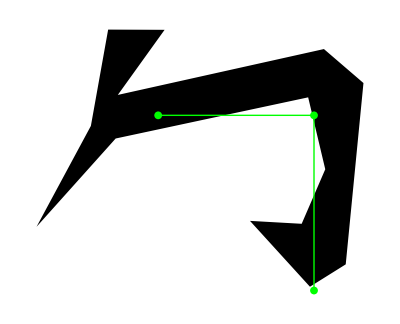

```mathematica
anchors={{10,-5},{50,-5},{50,-50}};
Graphics[{Polygon[Ts.Flatten[{anchors,1}]],Green,Line[anchors],Disk[#,1]&/@anchors}]
```

## 对比

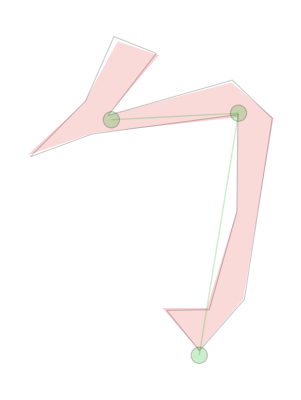
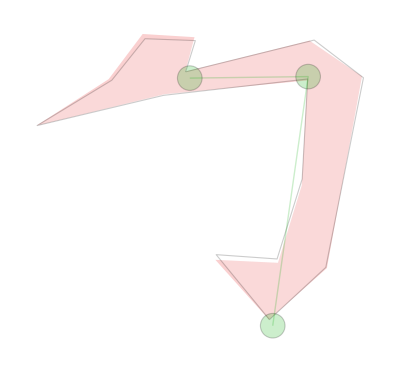
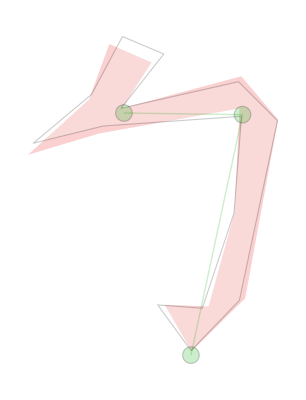
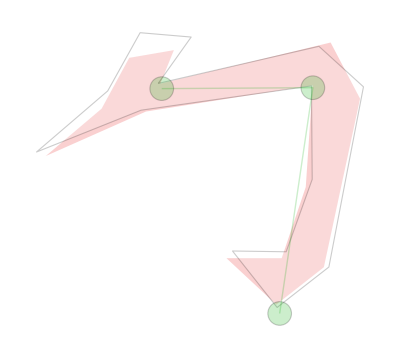
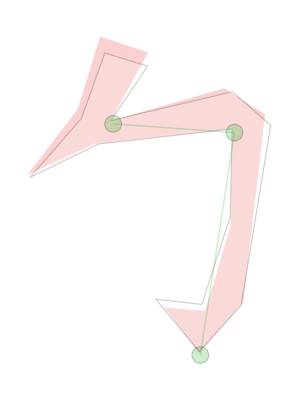
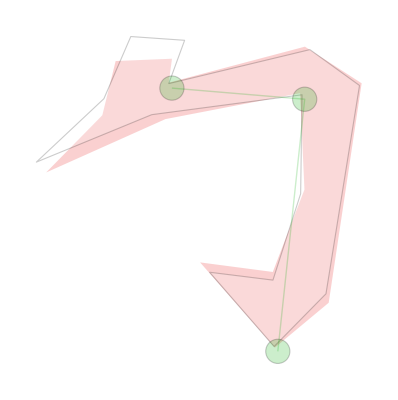
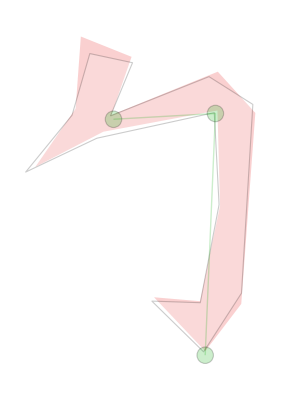
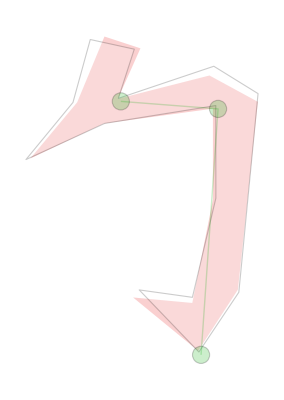

```mathematica
Graphics[{Hue[1,0.9,0.9,0.2],EdgeForm[None],Polygon[#⟦1⟧],EdgeForm[{Thick,Black}],FaceForm[White],Polygon[((Ts.Flatten[{(#⟦2⟧ᵀ-#⟦2,1⟧)ᵀ,1}])ᵀ+#⟦2,1⟧)ᵀ],Darker[Green],Line[#⟦2⟧],Disk[#,3]&/@#⟦2⟧}]&/@points
```

## 展示

```mathematica
DynamicModule[{p1={0,0},p2={50,-5},p3={50,-100}},Graphics[{Dynamic@Polygon[p1+#&/@(Ts.Flatten[{p1,p2,p3,1}])],Green,Dynamic@Line[{p1,p2,p3}],Dynamic[Disk[#,1]&/@{p1,p2,p3}],{Locator[Dynamic[p1]],Locator[Dynamic[p2]],Locator[Dynamic[p3]]}},PlotRange->All]]
```